```mathematica
(* Computing the curvature of a C. elegans worm 
M.Dies - MSB lab @ ICFO  *) 

(* I have used ideas and chunks of code from:
https://mathematica.stackexchange.com/questions/17060/image-processing-finding-orientation-and-position-of-symmetry-axes/17065
http://www.sciencedirect.com/science/article/pii/S0031320301000401#
 http://mathematica.stackexchange.com/questions/95425/can-i-get-the-curvature-at-any-point-of-a-random-curve/95442 
 and 
https://dsp.stackexchange.com/questions/25907/why-the-curvature-of-straight-line-in-curvature-scale-space-is-not-zero/25918#25918 *)

Remove["Global`*"]
SetDirectory["/Users/marta/Dropbox/ICFO/CurvatureTest_Marta/Portfolio"];
img=Import["worm_input_image.tif"]

(* First, I need to binarize the worm's image, and extract perimeter/contour. See the following documentation:
http://reference.wolfram.com/language/guide/SegmentationAnalysis.html 
and 
http://reference.wolfram.com/language/guide/BasicImageManipulation.html *)
contdet=ContourDetect[img,0.55];
contdet2=SelectComponents[contdet, Large] ;
contdet3=SelectComponents[contdet2,"Width",#>50&]
(* Converting binary image into an array of 0s and 1s*)
Tdata=ImageData[contdet3];
(* EdgeDetect might return edges that are thicker than one pixel, use Thinning to get single-pixel-wide edges *)
perimImg=Thinning[EdgeDetect[contdet3,10]]
(* Converting perimeter image into an array of 0s and 1s*)
TdataALLPerim=ImageData[perimImg];
(* Selecting only outer perimeter *)
OUTERPerimImg=Thinning[SelectComponents[perimImg,"PerimeterLength",#>500&]]
TdataPerim=ImageData[OUTERPerimImg];
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
(* The following function computes the center of mass, the inertia matrix, and the eigenvectors of the inertia matrix (that account for the axis of symmetry of the image). For this piece of code I've used ideas and chunks of code from: 
https://mathematica.stackexchange.com/questions/17060/image-processing-finding-orientation-and-position-of-symmetry-axes/17065 *)
findSym2[img_,img2_]:=
Module[{imd,imd2,points,weights,mass,pointsCom,diag,inertia,i,j},
imd=Transpose[img];
imd2=Transpose[img2];
{nx,ny}=Dimensions[imd];
points=Tuples[{Range[nx],Reverse@Range[ny]}];
weights=Flatten[imd];(* Assuming an homogeneous distribution of mass in the worm *)
mass=Total[weights];
com=Total[points weights]/mass//N; (* center of mass *)
pointsCom=(Subtract[#,com]&/@points) weights;
diag=Total[(#.#)&/@pointsCom];
(* Computing the inertia tensor *)
inertia=Table[KroneckerDelta[i,j] diag-Total[(#[[i]] #[[j]])&/@pointsCom],{i,1,2},{j,1,2}];
{v1,v2}=Eigenvectors[inertia];
{λ1,λ2}=Eigenvalues[inertia];
proportion=0.10;
(* Plotting segmentation + CM + symmetry axes *)
plot1=Graphics[{Inset[Image[Transpose@imd2],Automatic,Automatic,Scaled[1]],Blue,Thick,Line[{{com,proportion nx/2 v1+com},{com,nx/(2 proportion) v2+com}}],Red,PointSize[Medium],Point[com]},PlotRange->{{1,nx},{1,ny}}];
Export["geometricalAnalysis_worm_Portfolio.tiff",plot1];
Show[plot1]//Print]


findSym2[Tdata,TdataALLPerim]
If[λ1>λ2,linevect=v1,linevect=v2];
(* Equation of the symmetry axis line: 
http://mathworld.wolfram.com/Two-PointForm.html *)
{px1,py1}=com-proportion nx/9 linevect;
{px2,py2}=proportion nx/9 linevect+com;
```

-Graphics-

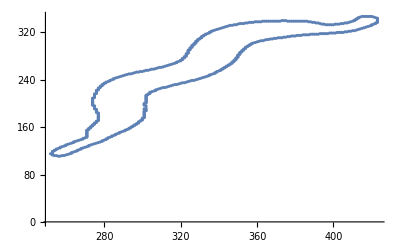

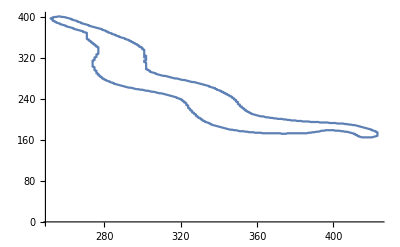

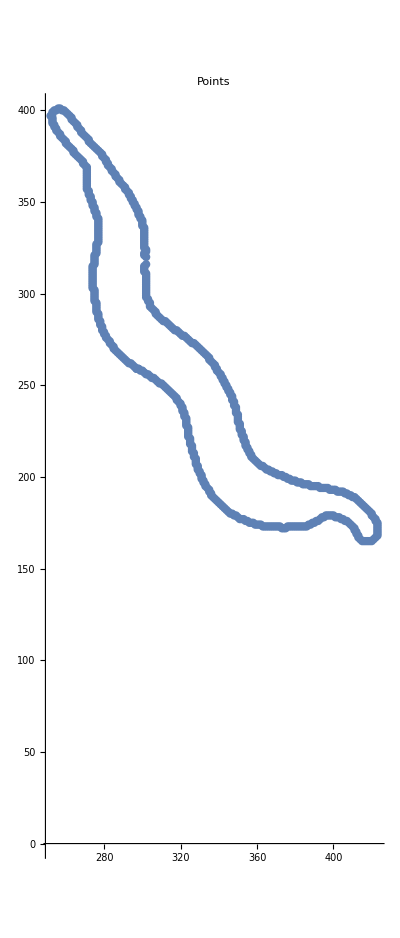
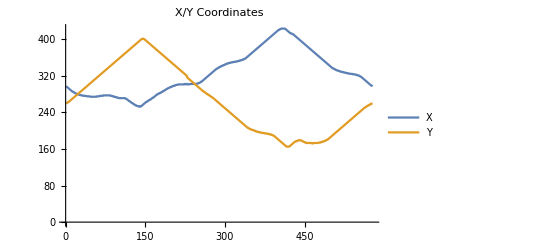

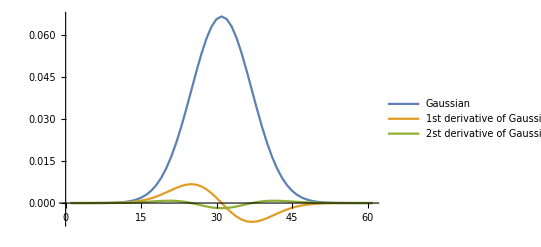

```mathematica
(* http://dsp.stackexchange.com/questions/25907/why-the-curvature-of-straight-line-in-curvature-scale-space-is-not-zero/25918#25918 *)
(* Curvature computation based on the following paper:
http://www.sciencedirect.com/science/article/pii/S0031320301000401# *)

(* Dimensions[TdataPerim] -> {512,612} *)
(* When working with Mathematica processed images, you'll need to transpose the image -> this line has to change: preperimPoints1=Flatten[Table[{x,y,TdataPerim[[x]][[y]]},{x,1,512},{y,1,612}],1];*)
preperimPoints1=Flatten[Table[{y,x,TdataPerim[[x]][[y]]},{x,1,512},{y,1,612}],1];
preperimPoints2=Select[preperimPoints1,#[[3]]≠0&];
perimPoints=preperimPoints2[[All,1;;2]];
pts=Table[{perimPoints[[i,1]],512-perimPoints[[i,2]]},{i,1,Length[perimPoints]}];
ListPlot[perimPoints]

(* Ordering perimeter points clockwise OR COUNTERCLOCKWISE: see 
http://mathematica.stackexchange.com/questions/61463/order-contour-points-in-clockwise 
The starting point is fixed as the left point having the same y as the centroid of the contour -this is, com-.*)
ContourBasedFeature[silhouette_,cofm_]:=Module[{centroid,startpoint,positions,contourPoints,order,clockwiseorder},
(centroid=cofm;
positions=pts;
startpoint=Select[positions,#[[2]]==Ceiling[centroid[[2]]]&&#[[1]]<Ceiling[centroid[[1]]]&];
contourPoints=Join[startpoint,DeleteCases[positions,startpoint//Flatten]];
order=contourPoints[[Last@FindShortestTour[contourPoints]]];
If[order[[1,2]]>order[[2,2]],Join[{order[[1]]},order[[Range[Length[order],2,-1]]]],order])];

whichorder=ContourBasedFeature[pts,com];
distX=0;
n=1;
While[distX==0,distX=whichorder[[n+1,1]]-whichorder[[n,1]];n++];
If[distX>0,pts=Reverse[whichorder][[1;;-2,All]],pts=whichorder[[2;;-1,All]]];

ListLinePlot[pts]

Row[{ListLinePlot[pts,AspectRatio->Automatic,Mesh->All,ImageSize->400,PlotLabel->"Points"],Spacer[50],ListLinePlot[Transpose[pts],PlotRange->All,PlotLabel->"X/Y Coordinates",PlotLegends->{"X","Y"},ImageSize->400]}]

(*Gaussian & derivatives; in the original paper (http://www.sciencedirect.com/science/article/pii/S0031320301000401#) σ=2 *)
σ=6; (* The higher σ, the smoother the perimeter (you need this to filter out noise). Be careful though, if the value it's too high you will end up loosing the image shape. *)

(* Sampling for the derivatives of gaussian should be the nearest odd number to 10*σ *)
halfSampling=Floor[10*σ/2];

g0=Table[1/(Sqrt[2 π] σ)*Exp[-x^2/(2 σ^2)],{x,-halfSampling,halfSampling}];
g1=Table[-x/(Sqrt[2 π] σ^3)*Exp[-x^2/(2 σ^2)],{x,-halfSampling,halfSampling}];
g2=Table[(-σ^2+x^2)/(Sqrt[2 π] σ^5)*Exp[-x^2/(2 σ^2)],{x,-halfSampling,halfSampling}];

ListLinePlot[{g0,g1,g2},PlotRange->All,PlotLegends->{"Gaussian","1st derivative of Gaussian","2st derivative of Gaussian"}]
```

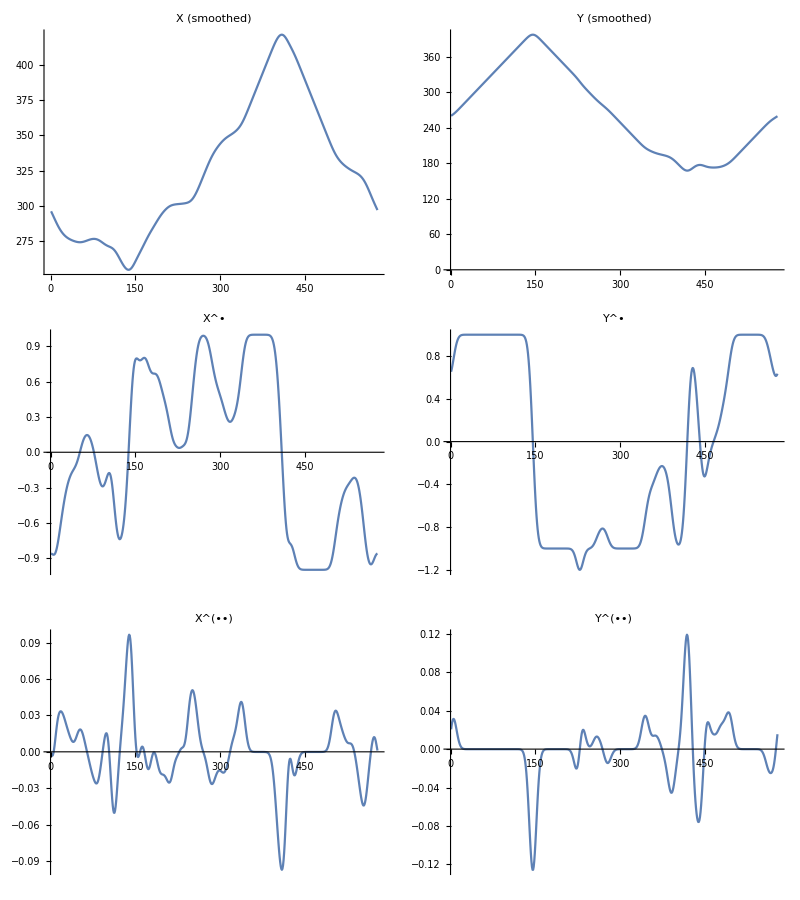

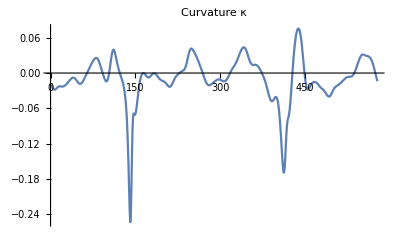

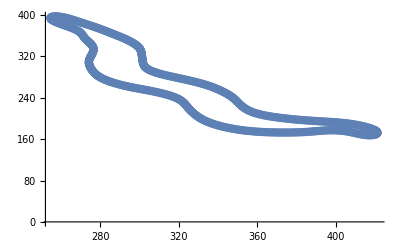

```mathematica
(*Convolve x and y with gaussian&derivatives*)
derivatives=Outer[ListConvolve[#1,#2,Round[Length[g1]/2]+1]&,{g0,g1,g2},Transpose[pts],1];

Grid[MapThread[ListLinePlot[#1,PlotRange->All,PlotLabel->#2]&,{derivatives,{{"X (smoothed)","Y (smoothed)"},{Overscript[X,•],Overscript[Y,•]},{Overscript[X,••],Overscript[Y,••]}}},2]]


{{xs,ys},{dx1,dy1},{dx2,dy2}}=derivatives;

(*calculate curvature*)
κ=dx1*dy2-dx2*dy1/((dx1^2+dy1^2)^(3/2));
ListLinePlot[κ,PlotRange->All,PlotLabel->"Curvature κ"]

ListLinePlot[Transpose[{xs,ys}],Mesh->All]
```

```mathematica
(* https://mathematica.stackexchange.com/questions/95425/can-i-get-the-curvature-at-any-point-of-a-random-curve/95442?utm_medium=organic&utm_source=google_rich_qa&utm_campaign=google_rich_qa *)
(*osculating circle animation*)
(* From: https://dsp.stackexchange.com/questions/25907/why-%20the-curvature-of-straight-line-in-curvature-scale-space-is-not-%20zero/25918#25918 *)
ListAnimate[Table[Row[{ListLinePlot[Transpose[{xs,ys}],AspectRatio-> Automatic,Mesh->All,ImageSize->400,BaseStyle-> {FontWeight-> "Bold",FontSize-> 15},PlotLabel->"Osculating circle r=1/κ",AxesLabel->{"X (pixels)","Y (pixels)"},
PlotRange->{{100,500},{100,500}}, 
(*PlotRange->{{xs[[DEB]]*0.95,xs[[DEB]]*1.05},{ys[[DEB]]*0.95,ys[[DEB]]*1.05}},*)
 Epilog->Module[{r,pt,n},(pt={xs[[DEB]],ys[[DEB]]};
r=Clip[1/κ[[DEB]],{-1,1}*10^4];
n=Normalize[{dy1[[DEB]],-dx1[[DEB]]}];
{Red,PointSize[Large],Point[pt],Circle[pt-n*r,r]})]],ListLinePlot[κ,PlotRange->{{1,Length[xs]+1},{-0.1,0.1}},PlotLabel->"Curvature κ (pixels^-1)",(*AxesLabel->{"Perimeter point (dimensionless)"},*)
ImageSize->400,BaseStyle-> {FontWeight-> "Bold",FontSize-> 15},
(*Epilog->{Red,Line[{{i,0},{i,10}}]}]}],{i,animationIdx}],i]*)
Epilog->{Red,Line[{{DEB,-15},{DEB,15}}]}]}],{DEB,1,Length[xs],10}]]
```

```mathematica
(* Final checking on smoothed perimeter used to compute curvature *)
ImageCompose[img,OUTERPerimImg]
Show[img,ListLinePlot[Transpose[{xs,ys}],Mesh->All]]
```

-Graphics-

-Graphics-